```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
NotebookDirectory[]
Off[Needs::nocont];Needs["LowDiscrep`"]; Needs["plots`"]; On[Needs::nocont];
SetOptions[#, Frame->True, Axes->False, FrameStyle->Thick, ImageSize->8*72, LabelStyle->{FontSize->25}] & /@ {Plot, ListPlot, ListLogLogPlot};
SeedRandom[1234];
```

/Users/npadmana/myWork/lowdiscrepancyRR/mma/

## Sec 2

### 1D low discrepancy vs regular comparisons

```mathematica
npts = 50;
```

```mathematica
region1d={Gray, Opacity[0.5],Polygon[{{0.0,0.0},{0.2,0}, {1.0, 0.8}, {1.0,1.0}, {0.8, 1.0}, {0.0,0.2}}]};
```

```mathematica
rr1 = ListPlot[generateRandomGrid[npts], AspectRatio->1, PlotRange->{{0,1},{0,1}}, Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
rr2 = ListPlot[RandomReal[{0,1},{npts^2,2}], AspectRatio->1, PlotRange->{{0,1},{0,1}}, Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
rr3 = ListPlot[generateLDSGrid[npts^2], AspectRatio->1, PlotRange->{{0,1},{0,1}}, Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
gg= {#1, #1+#2*0.4-0.2} &@@@generateLDSGrid[npts^2];
rr4 = ListPlot[gg, AspectRatio->1, PlotRange->{{0.0,1.0},{-0.2,1.2}},Prolog->region1d, PlotRangePadding->0.01];
```

```mathematica
Export["../tex/plots/grid1d-1.pdf", rr1];
Export["../tex/plots/grid1d-2.pdf", rr2];
Export["../tex/plots/grid1d-3.pdf", rr3];
Export["../tex/plots/grid1d-4.pdf", rr4];
```

```mathematica
Clear[gg, rr1, rr2, rr3, rr4, region1d]
```

### 1D interval comparison tests

### Angular cap convergence tests

### 3D Box comparison tests

## Sec 3

### Deep2 mask

```mathematica
(* Make a map of the DEEP2 mask *)
```

```mathematica
deep2 = Import["../data/deep2/windowf.31.fits","RawData"];
deep2meta = Import["../data/deep2/windowf.31.fits","Metadata"];
deep2 = Flatten[deep2, {{1,2},{3}}];
limits = ({{"RALIM0", "DECLIM0"}, {"RALIM1", "DECLIM1"}}/. deep2meta)[[All,All,1]];
ndim = ({"NRA","NDEC"}/.deep2meta)[[All,1]];
dlim = (limits[[2]] - limits[[1]])/ndim;
```

```mathematica
ndim
plotlim = Transpose[limits]- {{351.5,351.5}, {0,0}}
size = Transpose[plotlim][[2]] - Transpose[plotlim][[1]]
```

{1500,1000}

{{-0.129791,0.583069},{-0.103432,0.37705}}

{0.71286,0.480482}

```mathematica
p1 = ArrayPlot[deep2, Frame->False, PlotRangePadding->None, DataReversed->True];
```

```mathematica
p2 = Plot[None, {x, limits[[1,1]], limits[[2,1]]}, PlotRange->plotlim, FrameTicks->{Automatic, Automatic, Automatic, Automatic}, PlotRangePadding->0.005, FrameLabel->{"RA-351.5","Dec"}, AspectRatio->2/3, Epilog->Inset[p1, Transpose[plotlim][[1]],{0,0}, size]];
```

```mathematica
Export["../tex/plots/deep2mask.pdf", p2];
```

### DEEP2 fits

```mathematica
nptlist = {1000, 4000, 16000, 64000, 256000, 1024000, 4096000, 16384000};
bin0 = processbin["../data/deep2/rrdump", 0, nptlist];
bin4 = processbin["../data/deep2/rrdump",4, nptlist];
bin0prng = processbin["../data/deep2_prng/rrdump",0,nptlist];
bin4prng = processbin["../data/deep2_prng/rrdump", 4, nptlist];
```

```mathematica
err[bin_] := Transpose[{bin[[All,1,2]], bin[[All, 2,3]]}];
```

```mathematica
xticks = {{10^3,"10^3"}, {10^4,"10^4"}, {10^5,"10^5"}, {10^6, "10^6"}, {10^7,"10^7"}};
yticks = {{10^-2,"10^-2"}, {10^-3,"10^-3"}, {10^-4, "10^-4"}, {10^-5, "10^-5"}};
pticks = {{yticks, Automatic}, {xticks, Automatic}};
pdata = err /@ {bin0, bin4, bin0prng, bin4prng};
prange = {{700, 3*^7},{3 10^-5,5*10^-2}};
pmarkers = {{pDisk,0.04}, {pSquare,0.04},{pDisk, 0.04}, {pSquare, 0.04}};
pstyle = {{"MediumBlue"},{"Firebrick"}, {FaceForm[],EdgeForm[{Thick,"MediumBlue"}]},{FaceForm[],EdgeForm[{Thick,"Firebrick"}]}}/.ColorData["Legacy", "ColorRules"];
p1 = ListLogLogPlot[pdata, PlotRange->prange,PlotStyle->pstyle,PlotMarkers->pmarkers, FrameTicks->pticks, FrameLabel->{"N_pairs","Relative Error"} ];
p2 = LogLogPlot[20 n^-1, {n, 100, 10^8}, PlotStyle->{AbsoluteDashing[5], Thick, Gray}];
p3 = LogLogPlot[0.7 n^-0.5, {n, 100, 10^8}, PlotStyle->{AbsoluteDashing[10], Thick, Gray}];
Export["../tex/plots/deep2rrcomp1.pdf",Show[p1,p2, p3]];
```

## Scratch

```mathematica
bin4[[1,1,{3,4}]]*60.0
```

{7.5,15.}

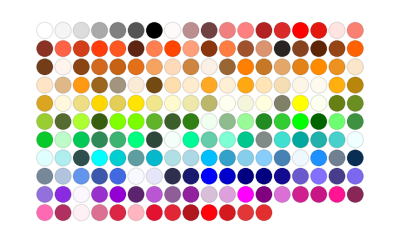

```mathematica
ColorData["Legacy","Panel"]
```